## Exact time evolution of a four-spin Heisenberg chain

Because we only treat four spins (leading to a Hilbert space of dimension 16), we can implement the time evolution operator exactly (and symbolically).

#### Time parameter

```mathematica
t=3/2
```

3/2

To minimize the Trotter error, we consider evolving only to t = 0.03.

```mathematica
t=3/100
```

3/100

### One-qubit states

```mathematica
ket0 = {{1},{0}}
```

{{1},{0}}

```mathematica
ket1={{0},{1}}
```

{{0},{1}}

```mathematica
psi0= KroneckerProduct[ket0,ket0,ket0,ket0]
```

{{1},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
keth = (1/Sqrt[2]) {{1},{1}}
```

{{1/(√2)},{1/(√2)}}

```mathematica
ketmin=(1/Sqrt[2]){{1},{-1}}
```

{{1/(√2)},{-1/(√2)}}

### Initial four-qubit states

```mathematica
psiunif = KroneckerProduct[keth,keth,keth,keth]
```

{{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4},{1/4}}

```mathematica
psising1=KroneckerProduct[ket0,ket1,ket0,ket1]
```

{{0},{0},{0},{0},{0},{1},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
psising2=KroneckerProduct[ket1,ket0,ket1,ket0]
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1},{0},{0},{0},{0},{0}}

```mathematica
psiclust=(1/2)(KroneckerProduct[keth,ket0,keth,ket0] + KroneckerProduct[keth,ket0,ketmin,ket1] + KroneckerProduct[ketmin,ket1,ketmin,ket0] + KroneckerProduct[ketmin,ket1,ketmin,ket1])
```

{{1/4},{1/4},{1/4},{-1/4},{1/4},{1/4},{-1/4},{-1/4},{1/4},{1/4},{1/4},{-1/4},{-1/4},{-1/4},{1/4},{1/4}}

### Pauli operators

```mathematica
X={{0,1},{1,0}}
```

{{0,1},{1,0}}

```mathematica
Y={{0,-I},{I,0}}
```

{{0,-ⅈ},{ⅈ,0}}

```mathematica
Z={{1,0},{0,-1}}
```

{{1,0},{0,-1}}

```mathematica
Id=IdentityMatrix[2]
```

{{1,0},{0,1}}

### Constructing the Hamiltonian

Now we can construct the Hamiltonian from its bond terms h. There are only three of these because each term h acts on two of the four qubits. We  also assume open boundary conditions.

```mathematica
h=KroneckerProduct[X,X]+KroneckerProduct[Y,Y]+KroneckerProduct[Z,Z]
```

{{1,0,0,0},{0,-1,2,0},{0,2,-1,0},{0,0,0,1}}

```mathematica
h1=KroneckerProduct[h,Id,Id]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,0,0,2,0,0,0,0,0,0,0},{0,0,0,0,0,-1,0,0,0,2,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,0,2,0,0,0,0,0},{0,0,0,0,0,0,0,-1,0,0,0,2,0,0,0,0},{0,0,0,0,2,0,0,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,2,0,0,0,-1,0,0,0,0,0,0},{0,0,0,0,0,0,2,0,0,0,-1,0,0,0,0,0},{0,0,0,0,0,0,0,2,0,0,0,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
h2=KroneckerProduct[Id,h,Id]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,2,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,0,2,0,0,0,0,0,0,0,0,0,0},{0,0,2,0,-1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,2,0,-1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,2,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,0,2,0,0},{0,0,0,0,0,0,0,0,0,0,2,0,-1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,2,0,-1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
h3=KroneckerProduct[Id,Id,h]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,2,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,2,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,2,-1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1,2,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,2,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,2,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,2,-1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
H=h1+h2+h3
```

{{3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,2,-1,0,2,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,2,0,0,0,0,0,0,0,0,0,0},{0,0,2,0,-1,0,0,0,2,0,0,0,0,0,0,0},{0,0,0,2,0,-3,2,0,0,2,0,0,0,0,0,0},{0,0,0,0,0,2,-1,0,0,0,2,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,2,0,0,0,0},{0,0,0,0,2,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,2,0,0,0,-1,2,0,0,0,0,0},{0,0,0,0,0,0,2,0,0,2,-3,0,2,0,0,0},{0,0,0,0,0,0,0,2,0,0,0,-1,0,2,0,0},{0,0,0,0,0,0,0,0,0,0,2,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,2,0,-1,2,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,2,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3}}

### The time evolution operator

```mathematica
Ut = MatrixExp[-I t H]
```

{{ⅇ^(-(9 ⅈ)/2),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},14,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,ⅇ^(-(9 ⅈ)/2)}}
 |  |  |  |

### The output states

The output states after time t = 3/2 are just the unitary operator multiplied by the given input state.

```mathematica
psiOut = Ut.psi0
```

{{ⅇ^(-(9 ⅈ)/2)},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
psiunifOut=FullSimplify[Ut.psiunif]
```

{{1/4 ⅇ^(-(9 ⅈ)/2)},{1/4 ⅇ^(-(9 ⅈ)/2)},{1/4 ⅇ^(-(9 ⅈ)/2)},{1/4 ⅇ^(-(9 ⅈ)/2)},{1/4 ⅇ^(-(9 ⅈ)/2)},{1/4 ⅇ^(-(9 ⅈ)/2)},{1/4 ⅇ^(-(9 ⅈ)/2)},{1/4 ⅇ^(-(9 ⅈ)/2)},{1/4 ⅇ^(-(9 ⅈ)/2)},{1/4 ⅇ^(-(9 ⅈ)/2)},{1/4 ⅇ^(-(9 ⅈ)/2)},{1/4 ⅇ^(-(9 ⅈ)/2)},{1/4 ⅇ^(-(9 ⅈ)/2)},{1/4 ⅇ^(-(9 ⅈ)/2)},{1/4 ⅇ^(-(9 ⅈ)/2)},{1/4 ⅇ^(-(9 ⅈ)/2)}}

```mathematica
psising1Out=FullSimplify[Ut.psising1]
```

{{0},{0},{0},{-1/12 ⅇ^(-(9 ⅈ)/2) (-2+2 ⅇ^(9 ⅈ) Cos[3 √3]+3 ⅈ √2 ⅇ^(6 ⅈ) Sin[3 √2])},{0},{1/24 ⅇ^(-3/2 ⅈ (3+2 (√2+√3))) (-2 (-2+√3) ⅇ^(3 ⅈ (3+√2))+2 (2+√3) ⅇ^(3 ⅈ (3+√2+2 √3))+ⅇ^(3 ⅈ √3) (-3 (-2+√2) ⅇ^(6 ⅈ)+4 ⅇ^(3 ⅈ √2)+3 (2+√2) ⅇ^(6 ⅈ (1+√2))))},{1/6 ⅇ^(-(9 ⅈ)/2) (1-ⅇ^(9 ⅈ) (Cos[3 √3]+ⅈ √3 Sin[3 √3]))},{0},{0},{1/6 ⅇ^(-(9 ⅈ)/2) (1-ⅇ^(9 ⅈ) (Cos[3 √3]+ⅈ √3 Sin[3 √3]))},{1/24 ⅇ^(-(9 ⅈ)/2) (4+3 (-2+√2) ⅇ^(-3 ⅈ (-2+√2))-3 (2+√2) ⅇ^(3 ⅈ (2+√2))+ⅇ^(9 ⅈ) (8 Cos[3 √3]+4 ⅈ √3 Sin[3 √3]))},{0},{1/24 ⅇ^(-(9 ⅈ)/2) (4-4 ⅇ^(9 ⅈ) Cos[3 √3]+6 ⅈ √2 ⅇ^(6 ⅈ) Sin[3 √2])},{0},{0},{0}}

```mathematica
psising2Out=FullSimplify[Ut.psising2]
```

{{0},{0},{0},{1/24 ⅇ^(-(9 ⅈ)/2) (4-4 ⅇ^(9 ⅈ) Cos[3 √3]+6 ⅈ √2 ⅇ^(6 ⅈ) Sin[3 √2])},{0},{1/24 ⅇ^(-(9 ⅈ)/2) (4+3 (-2+√2) ⅇ^(-3 ⅈ (-2+√2))-3 (2+√2) ⅇ^(3 ⅈ (2+√2))+ⅇ^(9 ⅈ) (8 Cos[3 √3]+4 ⅈ √3 Sin[3 √3]))},{1/6 ⅇ^(-(9 ⅈ)/2) (1-ⅇ^(9 ⅈ) (Cos[3 √3]+ⅈ √3 Sin[3 √3]))},{0},{0},{1/6 ⅇ^(-(9 ⅈ)/2) (1-ⅇ^(9 ⅈ) (Cos[3 √3]+ⅈ √3 Sin[3 √3]))},{1/24 ⅇ^(-3/2 ⅈ (3+2 (√2+√3))) (-2 (-2+√3) ⅇ^(3 ⅈ (3+√2))+2 (2+√3) ⅇ^(3 ⅈ (3+√2+2 √3))+ⅇ^(3 ⅈ √3) (-3 (-2+√2) ⅇ^(6 ⅈ)+4 ⅇ^(3 ⅈ √2)+3 (2+√2) ⅇ^(6 ⅈ (1+√2))))},{0},{-1/12 ⅇ^(-(9 ⅈ)/2) (-2+2 ⅇ^(9 ⅈ) Cos[3 √3]+3 ⅈ √2 ⅇ^(6 ⅈ) Sin[3 √2])},{0},{0},{0}}

```mathematica
psiclustOut=FullSimplify[Ut.psiclust]
```

{{1/4 ⅇ^(-(9 ⅈ)/2)},{1/4 ⅇ^(-(9 ⅈ)/2)},{1/4 ⅇ^(-(9 ⅈ)/2)},{1/12 ⅇ^((9 ⅈ)/2) (-3 Cos[3 √3]+ⅈ √3 Sin[3 √3])},{1/4 ⅇ^(-(9 ⅈ)/2)},{1/12 ⅇ^((9 ⅈ)/2) (3 Cos[3 √3]+ⅈ √3 Sin[3 √3])},{1/12 ⅇ^((3 ⅈ)/2) (-3-2 ⅈ √3 ⅇ^(3 ⅈ) Sin[3 √3])},{1/8 ⅇ^(-(9 ⅈ)/2) (-1+ⅇ^(6 ⅈ) (1-2 Cos[3 √2]+ⅈ √2 Sin[3 √2]))},{1/4 ⅇ^(-(9 ⅈ)/2)},{1/12 ⅇ^((3 ⅈ)/2) (3-2 ⅈ √3 ⅇ^(3 ⅈ) Sin[3 √3])},{1/12 ⅇ^((9 ⅈ)/2) (3 Cos[3 √3]+ⅈ √3 Sin[3 √3])},{1/8 ⅇ^(-(9 ⅈ)/2) (-1+ⅇ^(6 ⅈ) (-1+ⅈ √2 Sin[3 √2]))},{1/12 ⅇ^((9 ⅈ)/2) (-3 Cos[3 √3]+ⅈ √3 Sin[3 √3])},{-1/16 ⅇ^(-(9 ⅈ)/2) (2+ⅇ^(6 ⅈ) (2+2 ⅈ √2 Sin[3 √2]))},{1/8 ⅇ^(-(9 ⅈ)/2) (-1+ⅇ^(6 ⅈ) (1+2 Cos[3 √2]-ⅈ √2 Sin[3 √2]))},{1/4 ⅇ^(-(9 ⅈ)/2)}}

For ease of reading, we provide the numerical approximations of the outputs.

```mathematica
psiOutN = N[psiOut]
```

{{-0.210796+0.97753 ⅈ},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.}}

```mathematica
psising1N=N[psising1Out]
```

{{0.},{0.},{0.},{-0.33326+0.260999 ⅈ},{0.},{-0.0191642-0.182828 ⅈ},{0.231016+0.18483 ⅈ},{0.},{0.},{0.231016+0.18483 ⅈ},{-0.616079+0.313301 ⅈ},{0.},{0.295676+0.216398 ⅈ},{0.},{0.},{0.}}

```mathematica
psising2N=N[psising2Out]
```

{{0.},{0.},{0.},{0.295676+0.216398 ⅈ},{0.},{-0.616079+0.313301 ⅈ},{0.231016+0.18483 ⅈ},{0.},{0.},{0.231016+0.18483 ⅈ},{-0.0191642-0.182828 ⅈ},{0.},{-0.33326+0.260999 ⅈ},{0.},{0.},{0.}}

```mathematica
psiclustN=N[psiclustOut]
```

{{-0.0526989+0.244383 ⅈ},{-0.0526989+0.244383 ⅈ},{-0.0526989+0.244383 ⅈ},{-0.100393+0.1406 ⅈ},{-0.0526989+0.244383 ⅈ},{-0.149415-0.0867313 ⅈ},{0.232123-0.303243 ⅈ},{0.20043+0.104227 ⅈ},{-0.0526989+0.244383 ⅈ},{0.267492+0.195505 ⅈ},{-0.149415-0.0867313 ⅈ},{0.174741-0.258028 ⅈ},{-0.100393+0.1406 ⅈ},{-0.139726-0.235728 ⅈ},{-0.130047-0.0992362 ⅈ},{-0.0526989+0.244383 ⅈ}}

### Output probabilities

The probabilities of measuring each output are obtained by finding the squared modulus of each state in the output vector. We also give these numerically to make them readable.

```mathematica
NormSq[x_]=(Norm[x])^2
```

Norm[x]^2

```mathematica
probs=Map[NormSq,psiOut]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
probsUnif=Map[NormSq,psiunifOut]
```

{1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16,1/16}

```mathematica
probsSing1=N[Map[NormSq,psising1Out]]
```

{0.,0.,0.,0.179183,0.,0.0337934,0.0875304,0.,0.,0.0875304,0.477711,0.,0.134252,0.,0.,0.}

```mathematica
probsSing2=N[Map[NormSq,psising2Out]]
```

{0.,0.,0.,0.134252,0.,0.477711,0.0875304,0.,0.,0.0875304,0.0337934,0.,0.179183,0.,0.,0.}

```mathematica
probsClust=N[Map[NormSq,psiclustOut]]
```

{0.0625,0.0625,0.0625,0.0298471,0.0625,0.0298471,0.145837,0.0510357,0.0625,0.109774,0.0298471,0.0971131,0.0298471,0.0750911,0.0267601,0.0625}

### Output histograms

```mathematica
label={"0000","0001","0010","0011","0100","0101","0110","0111","1000","1001","1010","1011","1100","1101","1110","1111"}
```

{0000,0001,0010,0011,0100,0101,0110,0111,1000,1001,1010,1011,1100,1101,1110,1111}

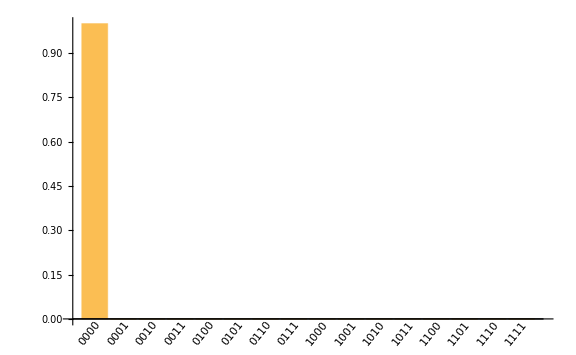

```mathematica
BarChart[probs,ChartLabels->Placed[label,{{0.5,0},{0.9,1}},Rotate[#,(2/7) Pi]&],ImageSize->Large]
```

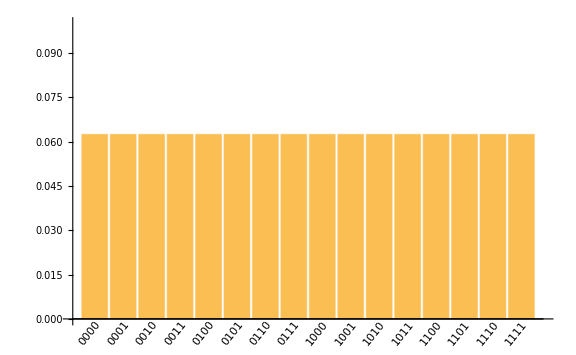

```mathematica
BarChart[probsUnif,ChartLabels->Placed[label,{{0.5,0},{0.9,1}},Rotate[#,(2/7) Pi]&],ImageSize->Large,PlotRange->{Automatic,{0,0.1}}]
```

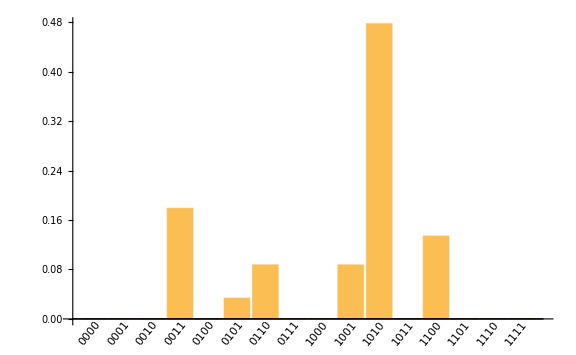

```mathematica
BarChart[probsSing1,ChartLabels->Placed[label,{{0.5,0},{0.9,1}},Rotate[#,(2/7) Pi]&],ImageSize->Large]
```

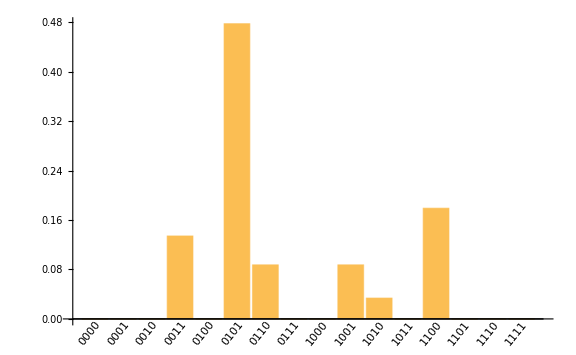

```mathematica
BarChart[probsSing2,ChartLabels->Placed[label,{{0.5,0},{0.9,1}},Rotate[#,(2/7) Pi]&],ImageSize->Large]
```

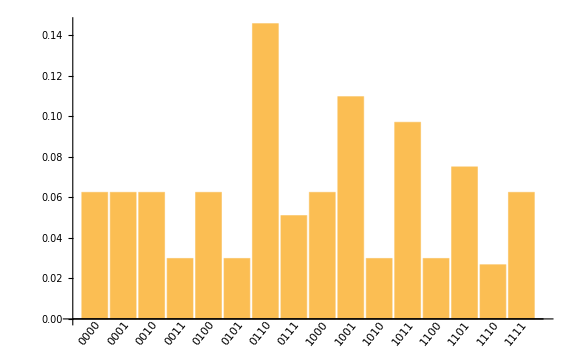

```mathematica
BarChart[probsClust,ChartLabels->Placed[label,{{0.5,0},{0.9,1}},Rotate[#,(2/7) Pi]&],ImageSize->Large]
```